```mathematica
SetDirectory@NotebookDirectory[]
<<"MagnetCode`"
Needs["MathPSfrag`"]
Needs["CustomTicks`"]
mm:=0.001
tesla:=1
```

/Users/will/magcode/examples

## Setup

```mathematica
mm:=0.001
tesla:=1
amps:=1
ohms:=1

magnet={
MagnetRadius->5mm,
MagnetLength->10mm,
Magnetisation->1 tesla
}
coil={
CoilRadius->7mm,
CoilLength->20mm,
Current->1 amps,
WireRadius->0.1mm,
WireCoating->0.01mm,
CoilResistance->8ohms
}
CalculateCoilParams[parameters__] := 
  ReleaseHold[{
               Hold@Symbol["CoilRadius"]->CoilRadius,
               Hold@Symbol["CoilThickness"]->CoilThickness,
               Hold@Symbol["CoilTurns"]->TotalTurns,
               Hold@Symbol["CoilLength"]->CoilLength,
               Hold@Symbol["Current"]->Current
              } //. 
  Flatten@{{
    CoilThickness -> ( 2 WireLength (WireRadius+WireCoating)^2 ) /
                                (  π CoilLength (CoilRadius+WireRadius+WireCoating) ) ,
    WireLength -> CoilResistance WireArea / WireResistivity ,
    WireResistivity -> 1.7*10^-8, (* copper *)
    WireArea -> π (WireRadius+WireCoating)^2,
    TotalTurns -> TurnsZ TurnsR,
    TurnsZ -> Round[CoilLength / (2WireRadius+2WireCoating)],
    TurnsR -> Round[CoilThickness / (2WireRadius+2WireCoating)]
    },parameters}//.{cm->0.01,mm->0.001,volts->1,ohms->1}]

CalculateCoilParams[coil]
```

{MagnetRadius→0.005,MagnetLength→0.01,Magnetisation→1}

{CoilRadius→0.007,CoilLength→0.02,Current→1,WireRadius→0.0001,WireCoating→0.00001,CoilResistance→8}

{CoilRadius→0.007,CoilThickness→0.000969041,CoilTurns→364,CoilLength→0.02,Current→1}

## Coil coil filament forces

These equations calculate the forces between two circular coils. The first for coaxial loops, the second including eccentricity. Want to ensure the latter converges to the former for eccentricity converging to zero.

```mathematica
With[{I=1,r=5mm,R=6mm,z=5mm,e=0.1mm},
{Timing@CoilCoilForce[I,I,r,R,z],Timing@CoilCoilForce[I,I,r,R,z,e]}
]
```

{{0.000115,-7.99888×10^-7},{0.047306,{-7.99631×10^-7,-1.30794×10^-8}}}

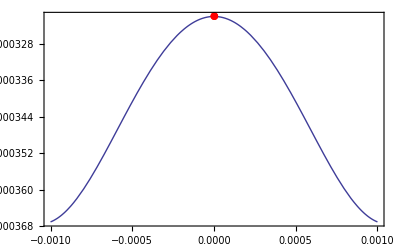

```mathematica
With[{I=1,r=5mm,R=6mm,z=1mm},
Show@{Plot[First@CoilCoilForce[I,I,r,R,z,e],{e,-1mm,1mm},Frame->True],ListPlot[{{0,CoilCoilForce[I,I,r,R,z]}},PlotStyle->Red,PlotMarkers->{Automatic,10}]}
]
```

## Comparison between different methods

Here we hope that a zero-thickness coil and a thin-thickness coil gives similar results.
Eccentricity should result in only small changes in force.

```mathematica
thinvthickparams={

MagnetRadius->9mm,
MagnetLength->10mm,
Magnetisation->1 tesla,

CoilRadius->10mm,
CoilLength->20mm,
CoilTurns->400,
Current->1,

Displacement->10mm,
IntegrationPrecision->3,
Verbose->True
};
```

```mathematica
Timing@MagnetCoilForce@{thinvthickparams}

Timing@MagnetCoilForce@{
thinvthickparams,
CoilThickness->0.1mm
}

Timing@MagnetCoilForce@{
thinvthickparams,
Method->Automatic,
CoilThickness->0.1mm
}

Timing@MagnetCoilForce@{
thinvthickparams,
CoilThickness->0.1mm,
Eccentricity->0.1mm
}
```

Coaxial thin coil:

{0.000645,2.60128}

Coaxial thick coil (Babic):

{0.04301,2.58611}

Coaxial thick coil (plain integral):

{0.018044,2.58613}

Eccentric thick coil:

{0.19284,2.53076}

```mathematica
thickfilamentparams:={

Displacement->10mm,
Eccentricity->0mm,

MagnetRadius->9mm,
MagnetLength->10mm,
Magnetisation->1,

CoilRadius->10mm,
CoilLength->20mm,
CoilThickness->5mm,

CoilTurns->100,
CoilTurnsR->5,
CoilTurnsZ->20,
Current->1,

Verbose->True

}
```

```mathematica
Timing@MagnetCoilForce@Flatten@{CoilThickness->0mm,Method->"Filament",thickfilamentparams}
Timing@MagnetCoilForce@Flatten@{CoilThickness->0mm,thickfilamentparams}//.thickfilamentparams
```

Coaxial thin coil: (filament)

{0.623455,-0.641207}

Coaxial thin coil:

{0.000666,-0.650321}

```mathematica
Timing@MagnetCoilForce@Flatten@{thickfilamentparams,Method->"Filament"}//.thickfilamentparams
Timing@MagnetCoilForce@Flatten@{thickfilamentparams,Method->"Shell"}//.thickfilamentparams
Timing@MagnetCoilForce@Flatten@{thickfilamentparams,Method->Automatic}//.thickfilamentparams
Timing@MagnetCoilForce@Flatten@{thickfilamentparams,Method->"Babic"}//.thickfilamentparams
```

Coaxial thick coil (filament):

{1.37966,-0.473645}

Coaxial thick coil (shell):

{0.001625,-0.497669}

Coaxial thick coil (plain integral):

{0.0128,-0.49944}

Coaxial thick coil (Babic):

{0.040737,-0.493784}

```mathematica
Timing@MagnetCoilForce@Flatten@{Eccentricity->0.5mm,thickfilamentparams,Method->"Filament"}//.thickfilamentparams
```

{445.86,{-0.474365,0.00284261}}

```mathematica
Timing@MagnetCoilForce@Flatten@{Eccentricity->0.5mm,thickfilamentparams,Method->Automatic}//.thickfilamentparams
```

Eccentric thick coil:

{0.208875,-0.450545}

## Thick coil speed tests

```mathematica
babicparams:={

MagnetRadius->9mm,
MagnetLength->10mm,
Magnetisation->1 tesla,

CoilRadius->10mm,
CoilThickness->1mm,
CoilLength->20mm,
CoilTurnsR->10,
CoilTurnsZ->40,
Current->1,

Displacement->10mm
}
```

```mathematica
Timing@MagnetCoilForce@{
babicparams,
Method->"Babic",
Verbose->True,
IntegrationPrecision->3
}
Timing@MagnetCoilForce@{
babicparams,
Method->Automatic,
Verbose->True,
IntegrationPrecision->3
}
Timing@MagnetCoilForce@{
babicparams,
Method->"Shell",
Verbose->True,
IntegrationPrecision->3
}
```

Coaxial thick coil (Babic):

{0.040359,-2.45444}

Coaxial thick coil (plain integral):

{0.014146,-2.45486}

Coaxial thick coil (shell):

{0.002694,-2.45475}

```mathematica
babicAccuracy = Table[
Flatten@{
Timing@MagnetCoilForce@{
babicparams,
Method->"Babic",
IntegrationPrecision->ii
},
Timing@MagnetCoilForce@{
babicparams,
IntegrationPrecision->ii
},
Timing@MagnetCoilForce@{
babicparams,
Method->"Shell",
IntegrationPrecision->ii
}}
,{ii,1,8}]
```

{{0.038466,-2.45444,0.011924,-2.4744,0.002566,-2.45475},{0.037132,-2.45444,0.013445,-2.45486,0.002572,-2.45475},{0.036943,-2.45444,0.01352,-2.45486,0.002584,-2.45475},{0.037431,-2.45444,0.020623,-2.45444,0.00261,-2.45475},{0.038085,-2.45444,0.023928,-2.45444,0.002545,-2.45475},{0.038218,-2.45444,0.035848,-2.45444,0.002608,-2.45475},{0.039007,-2.45444,0.058529,-2.45444,0.00259,-2.45475},{0.041084,-2.45444,0.142531,-2.45444,0.002733,-2.45475}}

```mathematica
TableForm[Map[InputForm,babicAccuracy,{2}]]
```

0.03846599999999967 | -2.4544407879895993 | 0.011924000000007595 | -2.4744006907978187 | 0.0025660000000016225 | -2.454751529717687
0.03713199999999972 | -2.4544407879895993 | 0.01344500000000437 | -2.4548594892044457 | 0.002572000000000685 | -2.454751529717687
0.03694299999999373 | -2.4544407879895993 | 0.013519999999999754 | -2.4548594892044457 | 0.0025839999999845986 | -2.454751529717687
0.037430999999997994 | -2.4544438306124783 | 0.020623000000014713 | -2.4544392729491915 | 0.00261000000000422 | -2.454751529717687
0.03808499999999526 | -2.4544438306124783 | 0.023928000000012162 | -2.454441045827852 | 0.002544999999997799 | -2.454751529717687
0.03821799999998632 | -2.4544438296675 | 0.035848000000001434 | -2.454443786446628 | 0.0026079999999950587 | -2.454751529717687
0.039006999999998015 | -2.454443830093919 | 0.05852899999999295 | -2.4544438175568843 | 0.0025900000000120826 | -2.454751529717687
0.04108400000001211 | -2.4544438300903315 | 0.1425310000000195 | -2.4544438299997147 | 0.0027330000000063137 | -2.454751529717687

```mathematica
100(2.454751529717687-2.4544438300903315)/2.4544438300903315
```

0.0125364

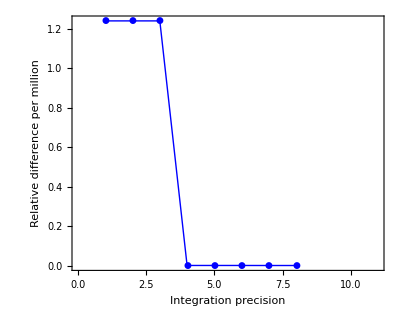
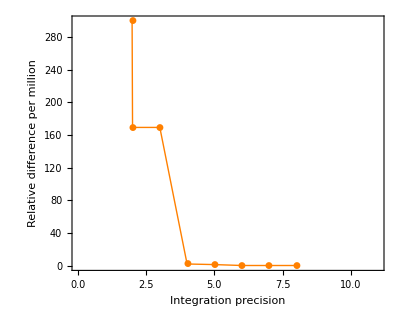

```mathematica
{ListPlot[1000000Abs@{1-babicAccuracy[[All,2]]/babicAccuracy[[-1,2]]},AspectRatio->0.8,PlotStyle->{Blue},PlotRange->{{0,11},Automatic},PlotMarkers->Automatic,Joined->True,Frame->True,Axes->False,FrameLabel->{"Integration precision","Relative difference per million"}],
ListPlot[1000000Abs@{1-babicAccuracy[[All,4]]/babicAccuracy[[-1,4]]},AspectRatio->0.8,PlotStyle->{Orange},PlotRange->{{0,11},{Automatic,300}},PlotMarkers->Automatic,Joined->True,Frame->True,Axes->False,FrameLabel->{"Integration precision","Relative difference per million"}]}
```

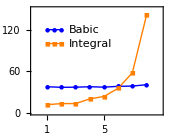

```mathematica
lx:={1,1.5,2,2.5}
ly={120,100};
prectiming=Show@{
ListPlot[1000{babicAccuracy[[All,1]],babicAccuracy[[All,3]]},PlotStyle->{Blue,Orange},PlotMarkers->{Automatic,6},Joined->True,PlotRange->{{0,9},{0,150}},Frame->True,FrameTicks->{Range[1,8],Automatic,None,None},Axes->False,AspectRatio->0.8,ImageSize->6 72/2.54,FrameLabel->{"Integration precision","Time, ms"}],
ListPlot[
{{{lx[[1]],ly[[1]]},{lx[[2]],ly[[1]]},{lx[[3]],ly[[1]]}},{{lx[[1]],ly[[2]]},{lx[[2]],ly[[2]]},{lx[[3]],ly[[2]]}}}
,PlotMarkers->{Automatic,6},PlotStyle->{Blue,Orange},Joined->True],
Graphics@Text["Babic",{lx[[4]],ly[[1]]},{-1,0}],
Graphics@Text["Integral",{lx[[4]],ly[[2]]},{-1,0}]
}
```

```mathematica
PSfragExport["fig/prec-timing",prectiming,RenumberTags->True]
```

{fig/prec-timing,fig/prec-timing-psfrag.eps,fig/prec-timing-psfrag.tex}

## Thick coil comparison graphs

### Thin coil

```mathematica
filamentparams={

MagnetRadius->9mm,
MagnetLength->10mm,
Magnetisation->1,

CoilRadius->10mm,
CoilLength->20mm,

CoilTurns->100,
Current->1

};
```

Single value test:

```mathematica
MagnetCoilForce@Flatten@{Displacement->10mm,Method->"Filament",filamentparams}//.filamentparams
MagnetCoilForce@Flatten@{Displacement->10mm,filamentparams}//.filamentparams
MagnetCoilForce@Flatten@{Displacement->10mm,CoilThickness->0.5mm,filamentparams}//.filamentparams
```

-0.641207

-0.650321

-0.631664

```mathematica
xmax:=40mm
dx:=1mm
Dx:=2dx
thinthin1=Table[{1000x,MagnetCoilForce@Flatten@{Displacement->x,Method->"Filament",filamentparams}},{x,dx,xmax,Dx}]
thinthin2=Table[{1000x,MagnetCoilForce@Flatten@{Displacement->x,filamentparams}},{x,0,xmax,dx}]
thinthin3=Table[{1000x,MagnetCoilForce@Flatten@{Displacement->x,CoilThickness->0.5mm,filamentparams}//.thickfilamentparams},{x,2dx,xmax,Dx}]
(* thinthin4=Table[{1000x,MagnetCoilForce@Flatten@{Displacement->x,CoilThickness->1mm,filamentparams}//.thickfilamentparams},{x,3dx,xmax,Dx}] *)
```

{{1.,-0.0601242},{3.,-0.194447},{5.,-0.377683},{7.,-0.546662},{9.,-0.626548},{11.,-0.640755},{13.,-0.591523},{15.,-0.458468},{17.,-0.302732},{19.,-0.208573},{21.,-0.149101},{23.,-0.109292},{25.,-0.0816999},{27.,-0.0621022},{29.,-0.0479113},{31.,-0.0374644},{33.,-0.0296594},{35.,-0.0237488},{37.,-0.0192167},{39.,-0.0157008}}

{{0.,0},{1.,-0.0617701},{2.,-0.127027},{3.,-0.199931},{4.,-0.285967},{5.,-0.388234},{6.,-0.485894},{7.,-0.557904},{8.,-0.606734},{9.,-0.636742},{10.,-0.650321},{11.,-0.648296},{12.,-0.630124},{13.,-0.593702},{14.,-0.534991},{15.,-0.451883},{16.,-0.365837},{17.,-0.298198},{18.,-0.246494},{19.,-0.206041},{20.,-0.173736},{21.,-0.147542},{22.,-0.126058},{23.,-0.108278},{24.,-0.0934538},{25.,-0.0810169},{26.,-0.0705252},{27.,-0.0616309},{28.,-0.0540568},{29.,-0.0475799},{30.,-0.0420193},{31.,-0.0372275},{32.,-0.0330836},{33.,-0.0294876},{34.,-0.0263568},{35.,-0.0236226},{36.,-0.0212272},{37.,-0.0191227},{38.,-0.0172684},{39.,-0.01563},{40.,-0.0141787}}

{{2.,-0.127707},{4.,-0.283929},{6.,-0.470325},{8.,-0.588056},{10.,-0.631664},{12.,-0.612145},{14.,-0.520883},{16.,-0.365988},{18.,-0.250182},{20.,-0.177452},{22.,-0.129296},{24.,-0.0961649},{26.,-0.0727631},{28.,-0.0558954},{30.,-0.0435296},{32.,-0.0343272},{34.,-0.0273848},{36.,-0.0220809},{38.,-0.0179809},{40.,-0.0147766}}

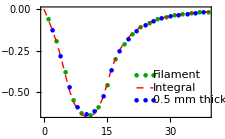

```mathematica
lx:={22,24,26}
ly=Table[i,{i,-0.4,-0.55,-0.075}];
styles={Darker[Green],{Dashed, Red},Blue,Orange};
joined={False,True,False};
markers={{Automatic,6},None,{Automatic,6}};

compareThinPlot=Show@{
ListPlot[{thinthin1},PlotMarkers->markers⟦1⟧,PlotStyle->styles⟦1⟧,Joined->joined⟦1⟧,
ImageSize->8 72/2.54,(* 6cm *)
Frame->True,
FrameLabel->{"Displacement, mm","Force, N"}],
ListPlot[{thinthin2},PlotMarkers->markers⟦2⟧,PlotStyle->styles⟦2⟧,Joined->joined⟦2⟧],
ListPlot[{thinthin3},PlotMarkers->markers⟦3⟧,PlotStyle->styles⟦3⟧,Joined->joined⟦3⟧],
(*ListPlot[{thinthin4},PlotMarkers->markers⟦4⟧,PlotStyle->styles⟦4⟧,Joined->joined⟦4⟧],*)
ListPlot[
{{{lx[[1]],ly[[1]]},{lx[[2]],ly[[1]]},{lx[[3]],ly[[1]]}}}
,PlotMarkers->markers⟦1⟧,PlotStyle->styles⟦1⟧,Joined->joined⟦1⟧],
ListPlot[
{{{lx[[1]],ly[[2]]},{lx[[2]],ly[[2]]},{lx[[3]],ly[[2]]}}}
,PlotMarkers->markers⟦2⟧,PlotStyle->styles⟦2⟧,Joined->joined⟦2⟧],
ListPlot[
{{{lx[[1]],ly[[3]]},{lx[[2]],ly[[3]]},{lx[[3]],ly[[3]]}}}
,PlotMarkers->markers⟦3⟧,PlotStyle->styles⟦3⟧,Joined->joined⟦3⟧],
(*ListPlot[
{{{lx[[1]],ly[[4]]},{lx[[2]],ly[[4]]},{lx[[3]],ly[[4]]}}}
,PlotMarkers->markers⟦4⟧,PlotStyle->styles⟦4⟧,Joined->joined⟦4⟧],*)
Graphics@Text[" Filament",{lx[[3]],ly[[1]]},{-1,0}],
Graphics@Text[" Integral",{lx[[3]],ly[[2]]},{-1,0}],
Graphics@Text[" 0.5 mm thick",{lx[[3]],ly[[3]]},{-1,0}]
(*Graphics@Text[" 1 mm thick",{lx[[3]],ly[[4]]},{-1,0}]*)
}
```

```mathematica
PSfragExport["fig/thin-compare",compareThinPlot];
```

### Thick coil

```mathematica
thickfilamentparams:={

Displacement->10mm,
Eccentricity->0mm,

MagnetRadius->9mm,
MagnetLength->10mm,
Magnetisation->1,

CoilRadius->10mm,
CoilLength->20mm,
CoilThickness->5mm,

CoilTurns->100,
CoilTurnsR->5,
CoilTurnsZ->20,
Current->1

}
```

```mathematica
xmax:=40mm
dx:=1.5mm
Dx:=2dx
thinthick1=Table[{1000x,MagnetCoilForce[Flatten@{Method->"Filament",Displacement->x,IntegrationPrecision->3,thickfilamentparams}]},{x,0dx,xmax,dx}]
thinthick2=Table[{1000x,MagnetCoilForce[Flatten@{Method->"Shell",Displacement->x,IntegrationPrecision->3,thickfilamentparams}]},{x,1dx,xmax,Dx}]
thinthick3=Table[{1000x,MagnetCoilForce[Flatten@{Displacement->x,Method->Automatic,IntegrationPrecision->3,thickfilamentparams}]//.thickfilamentparams},{x,2dx,xmax,Dx}]
thinthick4=Table[{1000x,MagnetCoilForce[Flatten@{Displacement->x,Method->"Babic",IntegrationPrecision->3,thickfilamentparams}]//.thickfilamentparams},{x,0,xmax,dx}]
```

{{0.,0},{1.5,-0.0761861},{3.,-0.156069},{4.5,-0.243116},{6.,-0.3348},{7.5,-0.408819},{9.,-0.456298},{10.5,-0.478114},{12.,-0.475077},{13.5,-0.447058},{15.,-0.394123},{16.5,-0.32498},{18.,-0.26358},{19.5,-0.213897},{21.,-0.174231},{22.5,-0.142632},{24.,-0.117407},{25.5,-0.0971951},{27.,-0.0809227},{28.5,-0.0677554},{30.,-0.0570446},{31.5,-0.0482853},{33.,-0.0410839},{34.5,-0.0351321},{36.,-0.0301876},{37.5,-0.0260592},{39.,-0.0225952}}

{{1.5,-0.0865854},{4.5,-0.27504},{7.5,-0.441957},{10.5,-0.499736},{13.5,-0.449461},{16.5,-0.314449},{19.5,-0.206902},{22.5,-0.138305},{25.5,-0.0945124},{28.5,-0.0660665},{31.5,-0.0472019},{34.5,-0.0344233},{37.5,-0.0255863}}

{{3.,-0.178854},{6.,-0.367523},{9.,-0.480651},{12.,-0.480759},{15.,-0.384914},{18.,-0.25727},{21.,-0.170246},{24.,-0.114832},{27.,-0.0792315},{30.,-0.0559155},{33.,-0.040316},{36.,-0.0296551},{39.,-0.0222187}}

{{0.,0},{1.5,-0.0875787},{3.,-0.178845},{4.5,-0.275189},{6.,-0.367508},{7.5,-0.437844},{9.,-0.480584},{10.5,-0.495865},{12.,-0.484194},{13.5,-0.446026},{15.,-0.384878},{16.5,-0.316759},{18.,-0.257311},{19.5,-0.208938},{21.,-0.17026},{22.5,-0.139438},{24.,-0.114831},{25.5,-0.095111},{27.,-0.0792305},{28.5,-0.0663759},{30.,-0.0559149},{31.5,-0.047356},{33.,-0.0403157},{34.5,-0.034494},{36.,-0.0296549},{37.5,-0.0256124},{39.,-0.0222186}}

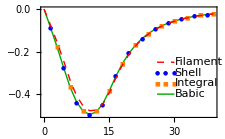

```mathematica
lx:={26,28,30}
ly=Table[i,{i,-0.25,-0.4,-0.05}];
comparePlot=Show@{
ListPlot[{thinthick4},Joined->True,PlotStyle->{Darker[Green]},
ImageSize->8 72/2.54,(* 6cm *)
Frame->True,
FrameLabel->{"Displacement, mm","Force, N"}],
ListPlot[{thinthick2,thinthick3},PlotMarkers->{Automatic,6},PlotStyle->{Blue,Orange}],
ListPlot[{thinthick1},Joined->True,PlotStyle->{Dashed,Red}],
ListPlot[{
{{lx[[1]],ly[[1]]},{lx[[2]],ly[[1]]},{lx[[3]],ly[[1]]}},
{{lx[[1]],ly[[4]]},{lx[[2]],ly[[4]]},{lx[[3]],ly[[4]]}}
},Joined->True,PlotStyle->{{Dashed,Red},{Dashing[1],Darker[Green]}}],
ListPlot[{
{{lx[[1]],ly[[2]]},{lx[[2]],ly[[2]]},{lx[[3]],ly[[2]]}},
{{lx[[1]],ly[[3]]},{lx[[2]],ly[[3]]},{lx[[3]],ly[[3]]}}
},PlotMarkers->{Automatic,6},PlotMarkers->{Automatic,6},PlotStyle->{Blue,Orange}],
Graphics@Text[" Filament",{lx[[3]],ly[[1]]},{-1,0}],
Graphics@Text[" Shell",{lx[[3]],ly[[2]]},{-1,0}],
Graphics@Text[" Integral",{lx[[3]],ly[[3]]},{-1,0}],
Graphics@Text[" Babic",{lx[[3]],ly[[4]]},{-1,0}]}
```

```mathematica
PSfragExport["fig/thickthin-compare",comparePlot];
```

## Eccentric displacement

```mathematica
param:={

MagnetRadius->9mm,
MagnetLength->10mm,
Magnetisation->1,

CoilRadius->11.5mm,
CoilLength->20mm,
CoilThickness->5mm,

CoilTurnsR->5,
CoilTurnsZ->20,
Current->1

}
```

```mathematica
Timing@MagnetCoilForce@Flatten@{param,
Method->"Filament",
Verbose->True,
RadialForce->False,
Displacement->2mm,
Eccentricity->2mm}
```

Eccentric thick coil: (filament)

{233.999,-0.0942}

```mathematica
Timing@MagnetCoilForce@Flatten@{param,
Verbose->True,
RadialForce->False,
Displacement->2mm,
Eccentricity->2mm}
```

Eccentric thick coil:

{0.055761,-0.111545}

### Integral method without and with eccentricity

Lone point should lie atop the curve

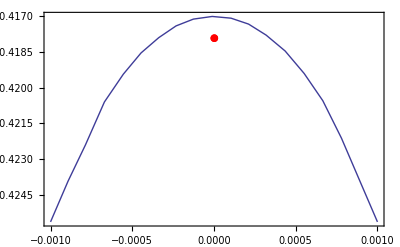

```mathematica
Show@{
Plot[MagnetCoilForce@Flatten[{param,Displacement->10mm,Eccentricity->e}],{e,-1mm,1mm},Frame->True,Axes->False,MaxRecursion->1,PlotPoints->10],ListPlot[{{0,MagnetCoilForce@Flatten[{param,Displacement->10mm}]}},PlotStyle->Red,PlotMarkers->{Automatic,10}]}
```

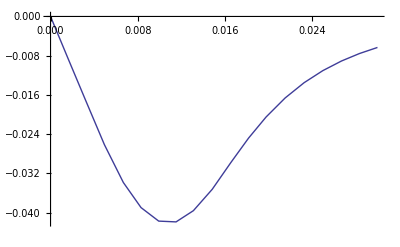

```mathematica
Plot[MagnetCoilForce@Flatten[{param,Displacement->x,Eccentricity->0mm}],{x,0mm,30mm},MaxRecursion->1,PlotPoints->10]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

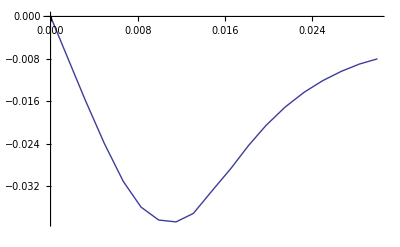

```mathematica
Plot[MagnetCoilForce@Flatten[{param,Displacement->x,Eccentricity->0.5mm}],{x,0mm,30mm},MaxRecursion->1,PlotPoints->10]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

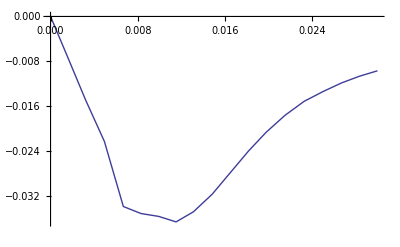

```mathematica
Plot[MagnetCoilForce@Flatten[{param,Displacement->x,Eccentricity->1mm}],{x,0mm,30mm},MaxRecursion->1,PlotPoints->10]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

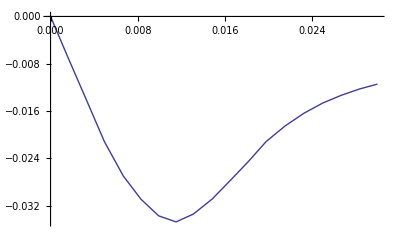

```mathematica
Plot[MagnetCoilForce@Flatten[{param,Displacement->x,Eccentricity->1.5mm}],{x,0mm,30mm},MaxRecursion->1,PlotPoints->10]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

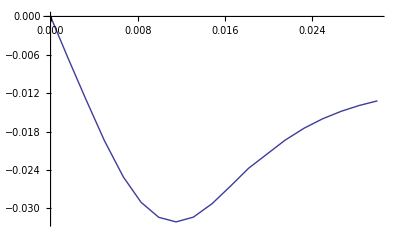

```mathematica
Plot[MagnetCoilForce@Flatten[{param,Displacement->x,Eccentricity->2mm}],{x,0mm,30mm},MaxRecursion->1,PlotPoints->10]
```

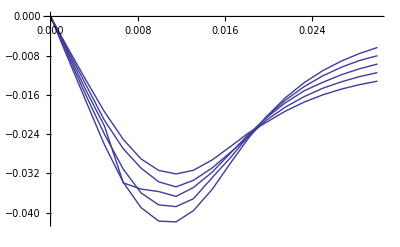

```mathematica
Show@{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
```

This takes AGES to execute:

```mathematica
h1=Plot[MagnetCoilForce@Flatten@{Method->"Filament",RadialForce->False,param,Displacement->x,Eccentricity->1.5mm},{x,0mm,30mm},PlotStyle->{Red,Dashed},MaxRecursion->1,PlotPoints->10]
```

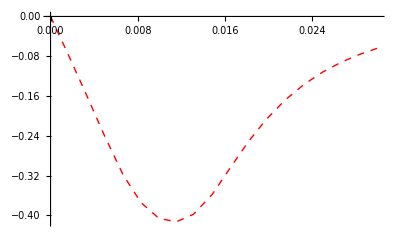

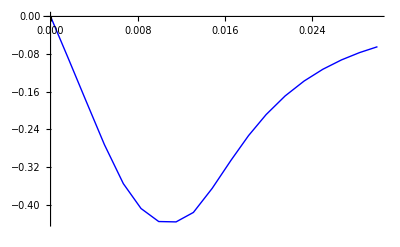

```mathematica
h2=Plot[MagnetCoilForce@Flatten@{RadialForce->False,param,Displacement->x,Eccentricity->1.5mm},{x,0mm,30mm},PlotStyle->{Blue},MaxRecursion->1,PlotPoints->10]
```

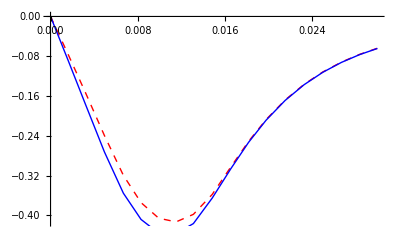

```mathematica
Show@{-Graphics-,-Graphics-}
```

## Radial forces

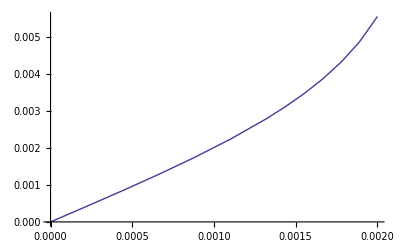

```mathematica
Plot[Last@MagnetCoilForce@Flatten[{Method->"Filament",param,Displacement->0mm,Eccentricity->x }],{x,0mm,2mm},MaxRecursion->1,PlotPoints->10]
```